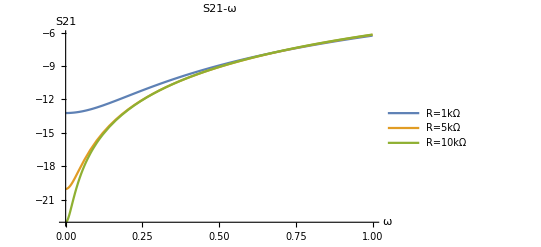

```mathematica
Plot[{10Log10[Abs[50/(50+1000/(1+50*(10^(-17))*1000*w*I))]],10Log10[Abs[50/(50+5000/(1+50*(10^(-17))*5000*w*I))]],10Log10[Abs[50/(50+10000/(1+50*(10^(-17))*10000*w*I))]]},{w,10^9,10^13},AxesLabel->{HoldForm[ω],HoldForm[S21]},AxesStyle->Black,PlotLegends->{"R=1kΩ","R=5kΩ","R=10kΩ"},PlotLabel->"S21-ω"]
```